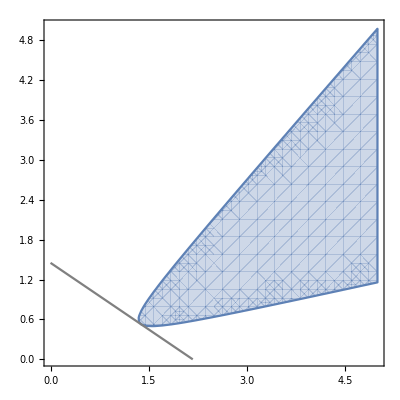

```mathematica
constraints = AllTrue[Eigenvalues[({{x1, x1 + ⅈ x2, x2 + 0.5}, {x1 - ⅈ x2, 5 x2, 0}, {x2 + 0.5, 0, x1 + x2}})], # ≥ 0 &];
feasible = RegionPlot[constraints, {x1, 0, 5}, {x2, 0, 5}];
H = 2 x1 + 3 x2;
H0 = FindMinimum[{2 x1 + 3 x2, constraints}, {x1, 5}, {x2, 5}]⟦1⟧;
Show[{feasible, ContourPlot[H == H0, {x1, 0, 5}, {x2, 0, 5}, ContourStyle->Gray]}]
```

```mathematica
FindMinimum[{2 x1 + 3 x2, constraints}, {x1, 5}, {x2, 5}]
```

{4.35069,{x1→1.38081,x2→0.529692}}